```mathematica
(*** PART 1: SENSITIVITY/SPECIFICITY CURVES ***)
```

```mathematica
(* a general function to load sensitivity/specificity data *) 
Clear[normalizeFirstCoord, getRateData];
normalizeFirstCoord[pointsList_]:= (
{#[[1]]/Max[pointsList[[All,1]]], #[[2]]} &/@ pointsList
) ; 
getRateData[filename_]:= (
file =  Import[NotebookDirectory[]<>filename]; 
lbsPts =Transpose@file[[{1,2}]];
ubsPts =Transpose@file[[{1,3}]];
joined = ubsPts~Join~Reverse@lbsPts; 
(* need to normalize them because the first coordinate is arbitrary numbers and the second one is [0,1] 
ASSUMING ALL FIRST COORDINATES MIN = 0 *) 
normalizeFirstCoord@ joined 
);
```

```mathematica
(* load the data *) 
majvoteSensPoints = getRateData["majvote_sensitivity.csv"]; (* aka majority vote *) 
majvoteSpecPoints = getRateData["majvote_specificity.csv"];
gm1SensPoints = getRateData["snorkel_sensitivity.csv"]; (* aka uninformed GM *) 
gm1SpecPoints = getRateData["snorkel_specificity.csv"]; 
gm2SensPoints = getRateData["snorkel_wCB_sensitivity.csv"]; (* aka informed GM *)
gm2SpecPoints = getRateData["snorkel_wCB_specificity.csv"];
sensActPts = normalizeFirstCoord@Transpose@Import[NotebookDirectory[]<>"true_sensitivity.csv"]; (* aka true rate *)
specActPts = normalizeFirstCoord@Transpose@Import[NotebookDirectory[]<>"true_specificity.csv"];
```

```mathematica
(* make the hulls *) 
sensMajvoteHull =Polygon[majvoteSensPoints];
specMajvoteHull =  Polygon[majvoteSpecPoints];
sensGm1Hull = Polygon[gm1SensPoints];
specGm1Hull = Polygon[gm1SpecPoints];
sensGm2Hull = Polygon[gm2SensPoints];
specGm2Hull = Polygon[gm2SpecPoints];
```

```mathematica
(* get the true rate line points outside of the hulls *)
outsideSensMajvotePts = Select[sensActPts, Not@RegionMember[sensMajvoteHull, #] & ];
outsideSpecMajvotePts = Select[specActPts, Not@RegionMember[specMajvoteHull, #] & ];
outsideSensGm1Pts = Select[sensActPts, Not@RegionMember[sensGm1Hull, #] & ];
outsideSpecGm1Pts = Select[specActPts, Not@RegionMember[specGm1Hull, #] & ];
outsideSensGm2Pts = Select[sensActPts, Not@RegionMember[sensGm2Hull, #] & ];
outsideSpecGm2Pts = Select[specActPts, Not@RegionMember[specGm2Hull, #] & ];
```

```mathematica
(* the coverage of the sensitivity true curve: majority vote, uninformed GM, informed GM *) 
1- ArcLength@Line@outsideSensMajvotePts/ArcLength@Line@sensActPts /. ArcLength[_]:> 0
1- ArcLength@Line@outsideSensGm1Pts/ArcLength@Line@sensActPts/. ArcLength[_]:> 0
1- ArcLength@Line@outsideSensGm2Pts/ArcLength@Line@sensActPts/. ArcLength[_]:> 0
```

1.

1.

1.

```mathematica
(* the coverage of the specificity true curve: majority vote, uninformed GM, informed GM *) 
1- ArcLength@Line@outsideSpecMajvotePts/ArcLength@Line@specActPts/. ArcLength[_]:> 0
1- ArcLength@Line@outsideSpecGm1Pts/ArcLength@Line@specActPts/. ArcLength[_]:> 0
1- ArcLength@Line@outsideSpecGm2Pts/ArcLength@Line@specActPts/. ArcLength[_]:> 0
```

0.66184

0.580478

1.

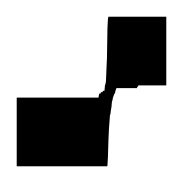

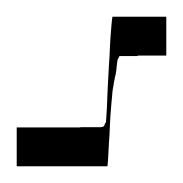

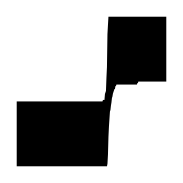

```mathematica
(* Debugging graphics for sensitivity *) 
Show[Graphics@sensMajvoteHull, ListPlot@outsideSensMajvotePts]
Show[Graphics@sensGm1Hull, ListPlot@outsideSensGm1Pts]
Show[Graphics@sensGm2Hull, ListPlot@outsideSensGm2Pts]
```

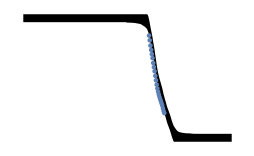

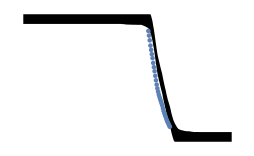

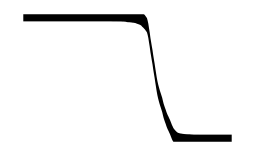

```mathematica
(* Debugging graphics for specificity *) 
Show[Graphics@specMajvoteHull, ListPlot@outsideSpecMajvotePts]
Show[Graphics@specGm1Hull, ListPlot@outsideSpecGm1Pts]
Show[Graphics@specGm2Hull, ListPlot@outsideSpecGm2Pts]
```

```mathematica
(*** PART 2: TRADEOFF CURVE ***)
```

```mathematica
(* load data for tradeoff curves (similar to ROC curves) *) 
rocMajvoteLB= Transpose@Import[NotebookDirectory[]<>"majvote_tradeoff_lb.csv"];
rocMajvoteUB= Transpose@Import[NotebookDirectory[]<>"majvote_tradeoff_ub.csv"];
rocMajvotePts = rocMajvoteLB~Join~rocMajvoteUB;
rocgm1LB= Transpose@Import[NotebookDirectory[]<>"snorkel_tradeoff_lb.csv"];
rocgm1UB= Transpose@Import[NotebookDirectory[]<>"snorkel_tradeoff_ub.csv"];
rocgm1Pts = rocgm1LB ~Join~rocgm1UB; 
rocgm2LB= Transpose@Import[NotebookDirectory[]<>"snorkel_wCB_tradeoff_lb.csv"];
rocgm2UB= Transpose@Import[NotebookDirectory[]<>"snorkel_wCB_tradeoff_ub.csv"];
rocgm2Pts = rocgm2LB ~Join~rocgm2UB; 

tprs= Import[NotebookDirectory[]<>"true_sensitivity.csv"][[2]]; 
tnrs= Import[NotebookDirectory[]<>"true_specificity.csv"][[2]]; 
rocRatePts = Transpose[{tnrs, tprs}];
```

```mathematica
(* construct the geometry, adding edge points for completeness
CANNOT USE CONVEX HULLS BECAUSE THE HULLS OF THESE CURVES ARE NOT CONVEX, SO NEED TO USE POLYGONS *) 
gm1Hull = Polygon[rocgm1UB~Join~{{0,1}}~Join~Reverse@rocgm1LB~Join~{{1,0}}];
gm2Hull =Polygon[rocgm2UB~Join~{{0,1}}~Join~Reverse@rocgm2LB~Join~{{1,0}}];
majvoteHull =Polygon[rocMajvoteUB~Join~{{0,1}}~Join~Reverse@rocMajvoteLB~Join~{{1,0}}];
rocLine = Line[rocRatePts];
```

```mathematica
(* take points outside of the hulls and drawing a line through them; 
possibly with some manual approximation *) 
outsideMajvotePts = Select[rocRatePts, Not@RegionMember[majvoteHull, #] & ];
(*outsideMajvotePts = outsideMajvotePts ~Join~{(5*{0.4817786693413573795`18.682847567782673,0.6464646464646465196`18.810544779386337}+4*outsideMajvotePts[[-1]])/9};*)

outsidegm1Pts = Select[rocRatePts, Not@RegionMember[gm1Hull, #] & ];
outsidegm1Pts = outsidegm1Pts ~Join~{(2*{0.5529923102641257637`18.742719092185208,0.5656565656565656353`18.75255283240865}+7*outsidegm1Pts[[-1]])/9};

outsidegm2Pts = Select[rocRatePts, Not@RegionMember[gm2Hull, #] & ];
(*outsidegm2Pts = outsidegm2Pts ~Join~{(4*{0.2848545636910732037`18.454623181735382,0.8585858585858585634`18.933783731116744}+5*outsidegm2Pts[[-1]])/9};*)

outsideMajvoteLine = Line@outsideMajvotePts; 
outsidegm1Line = Line@outsidegm1Pts;
outsidegm2Line = Line@outsidegm2Pts;
```

```mathematica
(* calculate line percentages contained in the hulls *)
```

```mathematica
1- ArcLength@outsideMajvoteLine/ArcLength@rocLine /. ArcLength[_]:> 0
1- ArcLength@outsidegm1Line/ArcLength@rocLine/. ArcLength[_]:> 0
1- ArcLength@outsidegm2Line/ArcLength@rocLine/. ArcLength[_]:> 0
```

1.

0.76125

1.

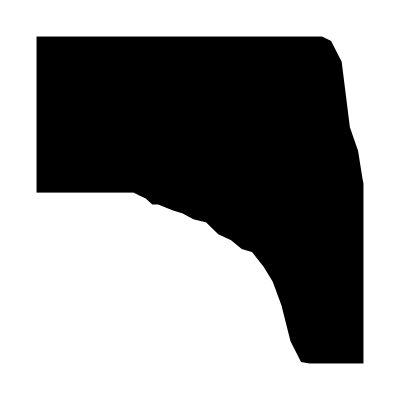

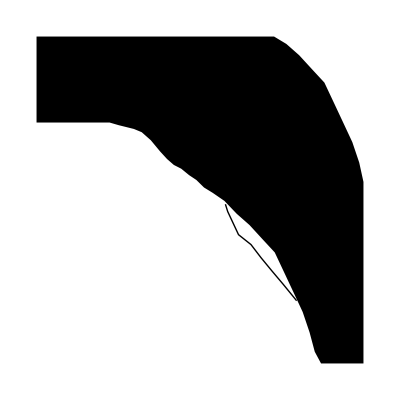

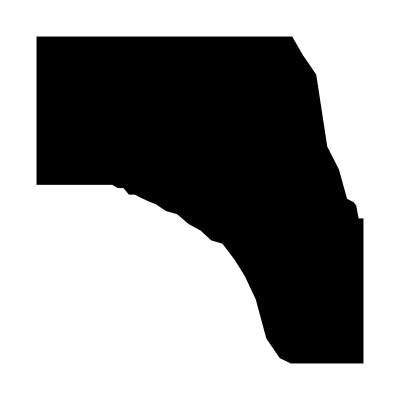

```mathematica
(* debugging graphics for tradeoff curves *) 
Show[Graphics@majvoteHull,Graphics@Line@outsideMajvotePts]
Show[Graphics@gm1Hull,Graphics@Line@outsidegm1Pts]
Show[Graphics@gm2Hull,Graphics@Line@outsidegm2Pts]
```